```mathematica
Clear["Global`*"]
SetDirectory["/Users/brycemorsky/Desktop/New projects/Norms and pandemics/figures"];
SetOptions[{Plot,ParametricPlot,ListPlot,ListLinePlot,ListPlot3D},PlotTheme->"Vibrant",BaseStyle->{FontSize->16},LabelStyle->Directive[FontSize->16],PlotStyle->Thickness[0.008]];
```

```mathematica
g[p_]=1/(1+p^η);
g[p_]=1-η*p;
u[i_,p_,q_] = -β*g[p]*i-c*p-θ*(p-q)^2;
(*BRD[i_,p_]=1/(1+Exp[κ*(u[i,0,p]-u[i,1,p])])-p;*)
BRD[i_,p_]=1/(1+Exp[κ*(c-i)])-p;
RD[i_,p_]=p*(1-p)*(u[i,1,p]-u[i,0,p]);
SEIR={s'[t]==-β*g[p[t]]*s[t]*i[t],e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
SEIRS={s'[t]==-β*g[p[t]]*s[t]*i[t]+α*(1-s[t]-e[t]-i[t]),e'[t]==β*g[p[t]]*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*BRD[i[t],p[t]]};
ics={s[0]==0.99,e[0]==0,i[0]==0.01,p[0]==0.01};
```

```mathematica
(* Parameters *)
α=0.01;
β=0.41;
γ=0.1;
δ=0.2;
ϵ=1;
κ=100;
(*c=0.025;*)
(*η=0.8;*)
```

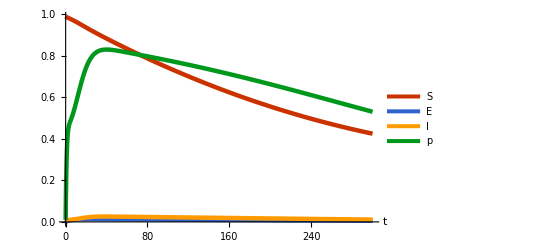

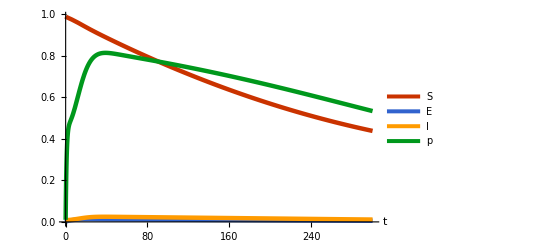

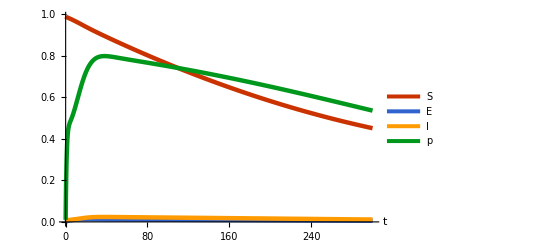

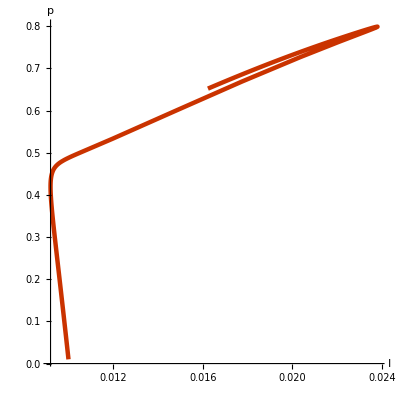

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.88},ics],{s,e,i,p},{t,0,1000}];
plt1=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.9},ics],{s,e,i,p},{t,0,1000}];
plt2=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.92},ics],{s,e,i,p},{t,0,1000}];
plt3=Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,300},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
plt4=ParametricPlot[Evaluate[{i[t],p[t]}/.sol],{t,0,200},PlotRange->Full,AspectRatio->1,AxesLabel->{"I","p"}]
(*Export["plt1.png",plt1,ImageResolution->200];
Export["plt2.png",plt2,ImageResolution->200];
Export["plt3.png",plt3,ImageResolution->200];
Export["plt4.png",plt4,ImageResolution->200];*)
```

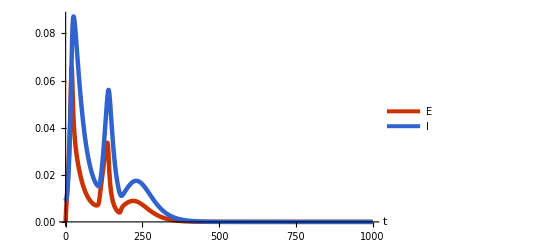

-Graphics-

-Graphics-

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.79},ics],{e,i},{t,0,1000}];
Plot[Evaluate[{e[t],i[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"E","I"},AxesLabel->{"t"}]
```

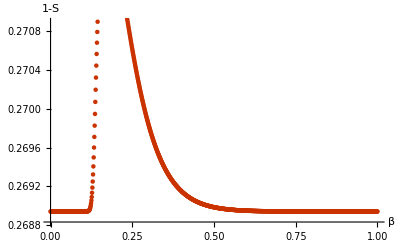

```mathematica
sfin=Array[n,{1001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.0,η->0.8,β->j/1000},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},Evaluate[{p[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt5=ListPlot[sfin,PlotStyle->PointSize[0.008],AxesLabel->{"β","1-S"}]
(*Export["plt5BR.png",plt5,ImageResolution->200];*)
```

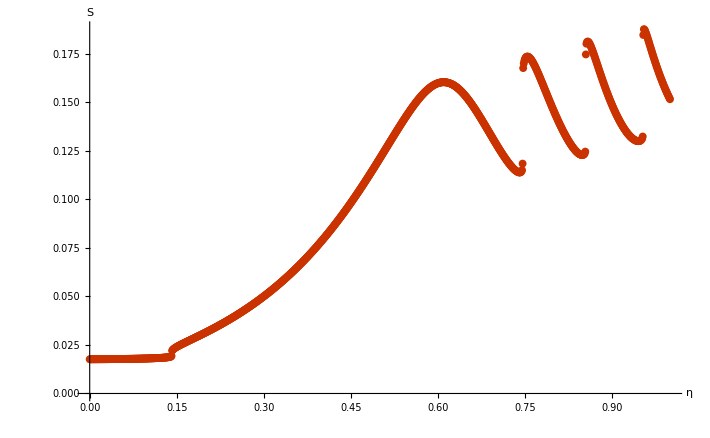

```mathematica
sfin=Array[n,{1001,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->j/1000,β->0.41},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{0.001*j},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{j,0,1000}];
plt5=ListPlot[sfin,PlotStyle->PointSize[0.008],AxesLabel->{"η","S"}]
(*Export["plt5BR.png",plt5,ImageResolution->200];*)
```

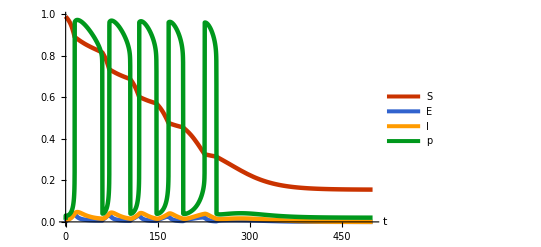

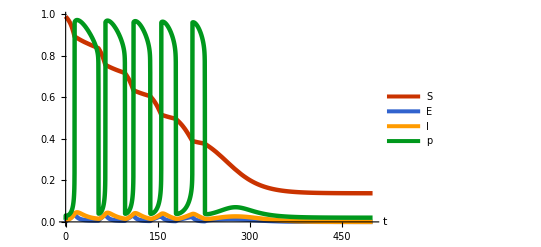

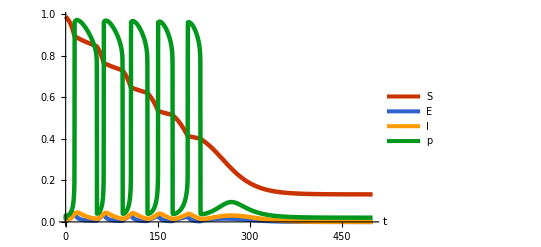

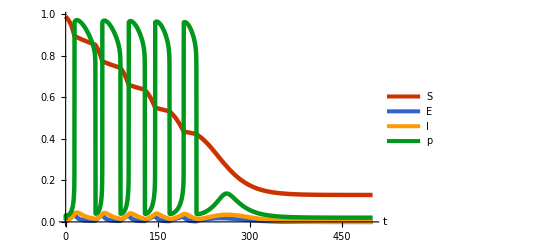

```mathematica
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.9},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.92},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.93},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
sol=NDSolve[Join[SEIR/.{c->0.01,θ->0.03,η->0.94},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,500},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```

```mathematica
sfin=Array[n,{40401,3}];
sfinrelief=Array[0&,{201,201}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->0.01,θ->j/2000,η->k/200},ics],{s,e,i,p},{t,0,1000}];
sfin[[count]]= Join[{j/2000},{k/200},Evaluate[{s[1000]}/.sol][[1]]];
sfinrelief[[j+1,k+1]]= Evaluate[{s[1000]}/.sol][[1]][[1]];
count=count+1;
,{j,0,200},{k,0,200}];
(*plt7 = ListPlot3D[sfin,AxesLabel->{"θ","c","S"}]*)
(*Export["plt7RD.png",plt7,ImageResolution->200]*)
```

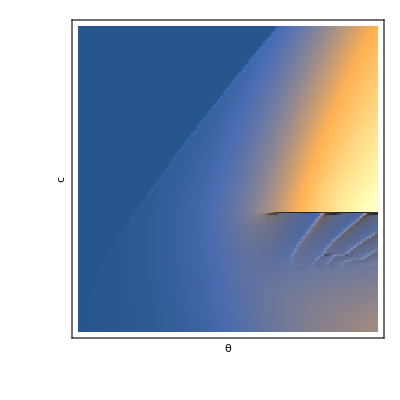

```mathematica
ReliefPlot[sfinrelief,AxesLabel->{"θ","c"}]
```

```mathematica
ListPlot3D[sfin,PlotRange->Full,AxesLabel->None]
ReliefPlot[sfinrelief,AxesLabel->{"θ","c"}]
```

-Graphics3D-

```mathematica
sfinc=Array[n,{40401,3}];
sfinreliefc=Array[0&,{201,201}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->j/2000,θ->0.03,η->k/200},ics],{s,e,i,p},{t,0,1000}];
sfinc[[count]]= Join[{j/2000},{k/200},Evaluate[{s[1000]}/.sol][[1]]];
sfinreliefc[[j+1,k+1]]= Evaluate[{s[1000]}/.sol][[1]][[1]];
count=count+1;
,{j,0,200},{k,0,200}];
(*plt7 = ListPlot3D[sfin,AxesLabel->{"θ","c","S"}]*)
(*Export["plt7RD.png",plt7,ImageResolution->200]*)
```

-Graphics3D-

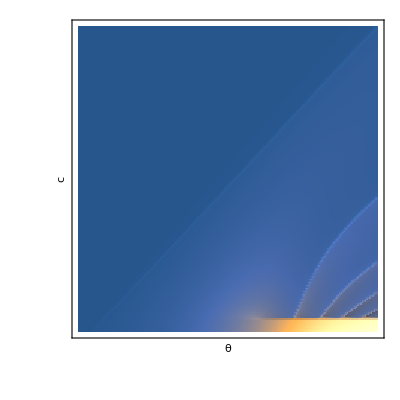

-Graphics3D-

```mathematica
ListPlot3D[sfinc,PlotRange->Full,AxesLabel->{"θ","c"}]
ReliefPlot[sfinreliefc,AxesLabel->{"θ","c"}]
```

```mathematica
sfinctheta=Array[n,{40401,3}];
sfinreliefctheta=Array[0&,{201,201}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->j/2000,θ->k/2000,η->0.95},ics],{s,e,i,p},{t,0,1000}];
sfinctheta[[count]]= Join[{j/2000},{k/2000},Evaluate[{s[1000]}/.sol][[1]]];
sfinreliefctheta[[j+1,k+1]]= Evaluate[{s[1000]}/.sol][[1]][[1]];
count=count+1;
,{j,0,200},{k,0,200}];
```

-Graphics3D-

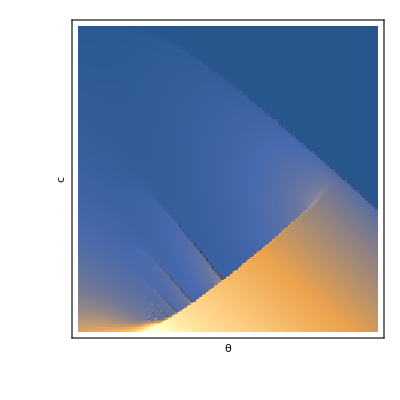

```mathematica
ListPlot3D[sfinctheta,PlotRange->Full,AxesLabel->{"θ","c"}]
ReliefPlot[sfinreliefctheta,AxesLabel->{"θ","c"}]
```

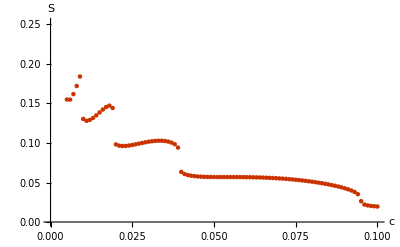

```mathematica
vtheta=Array[n,{501,2}];
count=1;
Do[
sol=NDSolve[Join[SEIR/.{c->k/1000,θ->0.03,η->0.95},ics],{s,e,i,p},{t,0,1000}];
vtheta[[count]]= Join[{0.001*k},Evaluate[{s[1000]}/.sol][[1]]];
count=count+1;
,{k,0,100}];
plt6=ListPlot[vtheta,PlotStyle->PointSize[0.008],AxesLabel->{"c","S"}]
(*Export["plt6.png",plt6,ImageResolution->200]*)
```

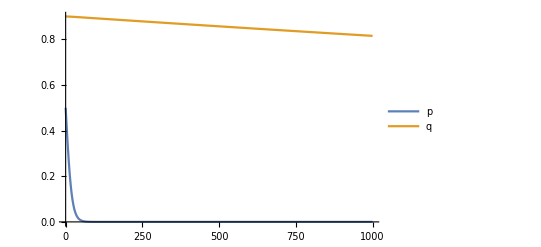

```mathematica
b=2;
c=1;
α=0.9;
ϵ=0.0001;
eqn={p'[t]==p[t]*(1-p[t])*(p[t]*(b-c+α*(1-q[t]))+(1-p[t])*(-c+α*(1-q[t]))-p[t]*(b-α*q[t])-(1-p[t])*(-α*q[t])),q'[t]==ϵ*(p[t]-q[t])};
ic={p[0]==0.5,q[0]== 0.9};
sols=NDSolve[Join[eqn,ic],{p,q},{t,0,1000}];
Plot[Evaluate[{p[t],q[t]}/.sols],{t,0,1000},PlotRange->All,PlotLegends->{"p","q"},AxesLabel->{"t"}]
```

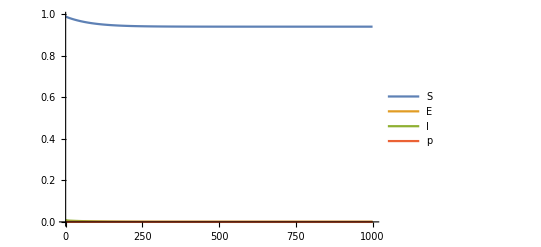

```mathematica
sol=NDSolve[Join[{s'[t]==-β*(1-m)*s[t]*i[t],e'[t]==β*(1-m)*s[t]*i[t]-δ*e[t],i'[t]==δ*e[t]-γ*i[t],p'[t]== ϵ*(1/(1+Exp[-100*(p[t]+θ*i[t]-1)])-p[t])}/.{m->0.79,c->20},ics],{s,e,i,p},{t,0,1000}];
Plot[Evaluate[{s[t],e[t],i[t],p[t]}/.sol],{t,0,1000},PlotRange->All,PlotLegends->{"S","E","I","p"},AxesLabel->{"t"}]
```